# cutoffs - varying ε

## fix smear and σ; calculate <g|ρ|g> for ε ϵ [5Ω,15Ω]; compare for different values of ε

## parameters

```mathematica
α=1;
Ω=1;
```

```mathematica
numSteps=10;
εMin=5Ω;εMax=15 Ω; εStepSize=Abs[εMin-εMax]/numSteps;
εValues=Table[ε,{ε,εMin,εMax,εStepSize}];
```

## smearing function

```mathematica
σ0=10^-4/Ω;
σ=σ0;
σNorm=σ/σ0;
```

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

## switching function

```mathematica
chiT1[t_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_]:=1/(r+T)
chiT3[t_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])
```

## k integrand

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-T/2-r,-T/2}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-T/2,T/2}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T/2,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,T/2,T/2+r}]
```

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrand[k_]:=-1/π*k*ftil[k]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

## cutoff function

```mathematica
gaussianCutoff[k_,ε_]:=ⅇ^((-Abs[k]^2)/(2 ε^2));
lorentzianCutoff[k_,ε_]:=ε^2/(Abs[k]^2+ε^2);
expCutoff[k_,ε_]:=ⅇ^((-Abs[k])/(2 ε));
sharpCutoff[k_,ε_]:=HeavisideTheta[k+ε,-k+ε];
```

```mathematica
Plot[gaussianCutoff[k,5
```

## <g|ρ|g>

```mathematica
T=2;r=0.2;
```

```mathematica
pGauss=Table[α+λ^2*NIntegrate[gaussianCutoff[k,ε] kIntegrand[k],{k,0,∞}],{ε,εMin,εMax,εStepSize}]
```

{0.997404,0.997197,0.997012,0.996842,0.996683,0.996535,0.996394,0.996261,0.996136,0.996017,0.995905}

```mathematica
pLor=Table[α+λ^2*NIntegrate[lorentzianCutoff[k,ε] kIntegrand[k],{k,0,∞}],{ε,εMin,εMax,εStepSize}]
```

{1-0.257454 λ^2,1-0.279769 λ^2,1-0.299007 λ^2,1-0.316073 λ^2,1-0.331507 λ^2,1-0.345655 λ^2,1-0.358748 λ^2,1-0.370951 λ^2,1-0.382387 λ^2,1-0.393147 λ^2,1-0.403307 λ^2}

```mathematica
pSharp=Table[α+λ^2*NIntegrate[kIntegrand[k],{k,0,ε}],{ε,εMin,εMax,εStepSize}]
```

{1-0.251991 λ^2,1-0.272116 λ^2,1-0.28957 λ^2,1-0.299624 λ^2,1-0.313162 λ^2,1-0.328038 λ^2,1-0.338197 λ^2,1-0.349603 λ^2,1-0.363224 λ^2,1-0.373653 λ^2,1-0.383999 λ^2}

```mathematica
pExp=Table[α+λ^2*NIntegrate[expCutoff[k,ε]*kIntegrand[k],{k,0,∞}],{ε,εMin,εMax,εStepSize}]
```

{1-0.27964 λ^2,1-0.303227 λ^2,1-0.323821 λ^2,1-0.342084 λ^2,1-0.358474 λ^2,1-0.373322 λ^2,1-0.386879 λ^2,1-0.399341 λ^2,1-0.410862 λ^2,1-0.421568 λ^2,1-0.431559 λ^2}

## plot

```mathematica
λ=0.1;Ω=.;
```

```mathematica
Clear[λ];
```

```mathematica
dataGauss=Transpose[{εValues,pGauss}];
dataLor=Transpose[{εValues,pLor}];
dataSharp=Transpose[{εValues,pSharp}];
dataExp=Transpose[{εValues,pExp}];
```

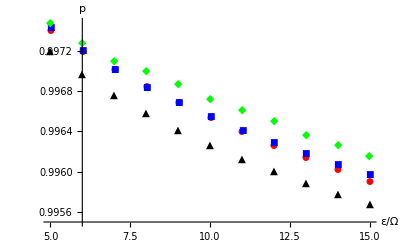

```mathematica
ListPlot[{dataGauss,dataLor,dataSharp,dataExp},
AxesLabel->{ε/Ω,p},
PlotStyle->{Red,Blue,Green,Black},
PlotMarkers->Automatic,
PlotLabel->Style["",FontSize->16]]
```

## relative differences

```mathematica
pGauss
```

{0.997404,0.997197,0.997012,0.996842,0.996683,0.996535,0.996394,0.996261,0.996136,0.996017,0.995905}

```mathematica
pLor
```

{0.997425,0.997202,0.99701,0.996839,0.996685,0.996543,0.996413,0.99629,0.996176,0.996069,0.995967}

```mathematica
pSharp
```

{0.99748,0.997279,0.997104,0.997004,0.996868,0.99672,0.996618,0.996504,0.996368,0.996263,0.99616}

```mathematica
pExp
```

{0.997204,0.996968,0.996762,0.996579,0.996415,0.996267,0.996131,0.996007,0.995891,0.995784,0.995684}

#### exp and gaussian

```mathematica
Abs[pExp[[6]]-pGauss[[6]]]/pExp[[6]]
```

0.000268801

```mathematica
Abs[pExp[[6]]-pGauss[[6]]]
```

0.000267798

#### exp and sharp

```mathematica
Abs[pExp[[6]]-pSharp[[6]]]/pExp[[6]]
```

0.000454536

```mathematica
Abs[pExp[[6]]-pSharp[[6]]]
```

0.000452839

#### exp and lorentzian

```mathematica
Abs[pExp[[6]]-pLor[[6]]]/pExp[[6]]
```

0.000277706

```mathematica
Abs[pExp[[6]]-pLor[[6]]]
```

0.000276669

#### gaussian and sharp

```mathematica
Abs[pGauss[[6]]-pSharp[[6]]]/pGauss[[6]]
```

0.000185685

```mathematica
Abs[pGauss[[6]]-pSharp[[6]]]
```

0.000185041

#### gaussian and lorentzian

```mathematica
Abs[pGauss[[6]]-pLor[[6]]]/pGauss[[6]]
```

8.9018×10^-6

```mathematica
Abs[pGauss[[6]]-pLor[[6]]]
```

8.87096×10^-6

#### sharp and lorentzian

```mathematica
Abs[pSharp[[6]]-pLor[[6]]]/pLor[[6]]
```

0.000176781

```mathematica
Abs[pSharp[[6]]-pLor[[6]]]
```

0.00017617

## save the data!!

```mathematica
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pGaussvEpsilon.csv",dataGauss];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pLorvEpsilon.csv",dataLor];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pSharpvEpsilon.csv",dataSharp];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pExpvEpsilon.csv",dataExp];
```